# Optimizing population bottlenecks

## Exact Solution

Define the variables:

```mathematica
d = Symbol["d"]; (*dilution ratio*)
r=Symbol["r"]; (*growth rate*)
t=Symbol["t"]; (*time at which mutation occurs*)
s=Symbol["s"]; (*selective benefit of mutation*)
```

Create some useful helper expressions to simplify the notation:

```mathematica
tau = - Log[d]/r; (*length of growth period*)
b=Exp[-r*(tau-t)*(1+s)]; (*inverse of expected number of mutants at the end of the growth period*)
g=(1-b)*(1-d);
```

Calculate the probability of i mutants remaining after the bottleneck. We need to define i=0 separately.

```mathematica
P[i_]=b(1-d)(d/(1-d))^i * Sum[g^(j-1)*Binomial[j,i],{j,i,Infinity}];
p0 = b (1-d) Sum[g^(j-1)*Binomial[j,0],{j,1,Infinity}];
```

Define v0s as the nontrivial solution to the infinite sum equation

```mathematica
solution = Solve[v0s==p0+Sum[P[i]*v0s^i,{i,1,Infinity}]/.t->0,v0s];
v0s=v0s/. Select[solution,#=!={v0s->1}&][[1]]
```

((-1+d) d^s)/(-1+d^(1+s))

Using v0s, find the chance of extinction for any t and s, V(t,s).

```mathematica
v = Simplify[p0+Sum[P[i]*v0s^i,{i,1,Infinity}]]
```

((-1+d) d^s ⅇ^(r (1+s) t))/(-1+d^(1+s) ⅇ^(r (1+s) t)-d^s (-1+ⅇ^(r (1+s) t)))

Find the rate of mutations occurring at time t and selective benefit s that will eventually fix (we ignore the population size and mutation rate here, the fixation rate is simply proportional to their product).

```mathematica
integrand = Simplify[d r Exp[r t](1-v)/tau]
```

-(d (-1+d^s) ⅇ^(r t) r^2)/((-1+d^(1+s) ⅇ^(r (1+s) t)-d^s (-1+ⅇ^(r (1+s) t))) Log[d])

Find the expected number of mutants that will occur and go onto fix in one growth period, conditional on them having selective benefit s.

```mathematica
gammagivens = Integrate[integrand,{t,0,tau},Assumptions->{r>0,d>0,d<1,t>0,s>0}]
```

(-r Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-(-1+d)/(d (-1+d^s))]+d r Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-((-1+d) d^s)/(-1+d^s)])/Log[d]

Note that there is no exact closed form integral available over values of s.

```mathematica
gamma = Integrate[gammagivens*a*Exp[-a*s],{s,0,Infinity}]
```

∫_0^∞ (a ⅇ^(-a s) (-r Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-(-1+d)/(d (-1+d^s))]+d r Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-((-1+d) d^s)/(-1+d^s)]))/Log[d]ⅆs

## Approximations

We can make some improvements to the integrand expression. First we can simplify it somewhat further than Mathematica does natively:


We can now use the change of variable  and the constant  to get:

First confirm that this really is an appropriate transformation:

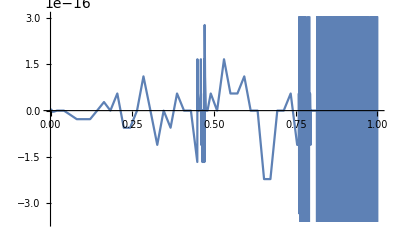

```mathematica
theta = (1/d -1)/(1 - d^s);
u = Symbol["u"] ;
gammagivens2= Simplify[1/tau Integrate[1/(theta u^(1+s) + 1),{u,d,1}, Assumptions -> {r>0, d>0, d<1, s>0}]];
Plot[Evaluate[{gammagivens-gammagivens2/r} /.{r->1, s->1}],{d,0.0001,1}]
```

Using the fact that theta is large and s is small, we can use the approximation:

We can now make a further approximation using the Taylor series for the exponential function:  
 
We can now observe that this is very close to the exact solution for all values of d and small values of s. The coarser approximation with a square root fails for small d.

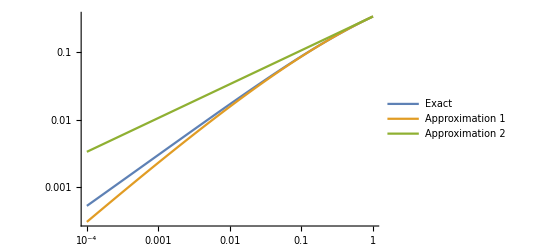

```mathematica
LogLogPlot[Evaluate[{gammagivens,r s/(1+s) Log[1/d]/(1/d-1), r s Sqrt[d] /(s+1)}/. {r->1,s->0.5}],{d,0.0001,1}, PlotLegends->{"Exact","Approximation 1","Approximation 2"}]
```

We can now approximate gamma unconditional on s. We have that  which does not have an elementary solution, but can be well approximated by :

```mathematica
q = Integrate[s/(1+s)/w*Exp[-s /w],{s,0,Infinity}, Assumptions -> {Re[w]>0}]
```

1-(ⅇ^(1/w) Gamma[0,1/w])/w

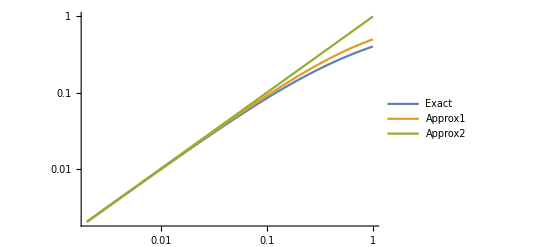

```mathematica
LogLogPlot[{q,w/(1+w),w},{w,.002,1}, PlotLegends->{"Exact","Approx1","Approx2"}]
```

Thus, the approximations used in the main text are well-justified.

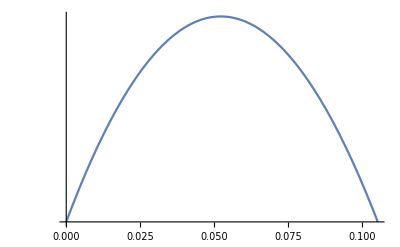

```mathematica
LogPlot[Evaluate[integrand/. {r->1,s->0.1,d->0.9}],{t,0,tau/.{r->1,d->0.9}}]
```